```mathematica
logicFile = FileNameJoin[{NotebookDirectory[],"Logic_results.txt"}]
reactFile = FileNameJoin[{NotebookDirectory[],"Reactive_results.txt"}]
```

/home/byrdie/School/Classes/CSCI446_Artificial_Intelligence/CSCI446_Artificial_Intelligence_Project2_Wumpus/src/Results/Logic_results.txt

/home/byrdie/School/Classes/CSCI446_Artificial_Intelligence/CSCI446_Artificial_Intelligence_Project2_Wumpus/src/Results/Reactive_results.txt

```mathematica
dat=ReadList[logicFile,Number,RecordLists->True];
```

```mathematica
dats=ReadList[reactFile,Number,RecordLists->True];
```

```mathematica
ListPointPlot3D[dat,PlotStyle->PointSize[Large]]
ListPointPlot3D[datr,PlotStyle->PointSize[Large]]
```

-Graphics3D-

ListPointPlot3D::arrayerr: datr must be a valid array or a list of valid arrays.

ListPointPlot3D[datr,PlotStyle→PointSize[Large]]

```mathematica
numobs = 40
numsteps = 7
stepsize=5
```

40

7

5

```mathematica
orgdata = Array[{},{numsteps,numobs}];
orgdatar = Array[{},{numsteps,numobs}];
Ndata = Array[{},numsteps];
Ndatar = Array[{},numsteps];
```

```mathematica
For[i = 1, i<=numsteps,i++,
For[j = 1, j <= numobs, j++,
For[k = 1, k <= Length[dat], k++,
If[dat[[k,1]]==(i*stepsize)∧dat[[k,2]]==j,orgdata[[i,j,0]]=Append[orgdata[[i,j,0]],dat[[k,3]]]];
If[dat[[k,1]]==(i*stepsize),Ndata[[i,0]]=Append[Ndata[[i,0]],dat[[k,3]]]];
]
]
]
For[i = 1, i<=numsteps,i++,
For[j = 1, j <= numobs, j++,
For[k = 1, k <= Length[datr], k++,
If[datr[[k,1]]==(i*stepsize)∧datr[[k,2]]==j,orgdatar[[i,j,0]]=Append[orgdatar[[i,j,0]],datr[[k,3]]]];
If[datr[[k,1]]==(i*stepsize),Ndatar[[i,0]]=Append[Ndatar[[i,0]],datr[[k,3]]]];
]
]
]
```

```mathematica
test={};
For[i = 1, i<=numsteps,i++,
For[j = 1, j <= numobs, j++,
 test = Append[test,{i*stepsize,j,Mean[orgdata[[i,j,0]]]}]
]
]
```

```mathematica
ListPlot3D[test, Mesh->All,AxesLabel->{"Size of Board","Number of Obstacles",  "Score"},ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
avedatar={};
```

```mathematica
For[i = 1, i<=numsteps,i++,
For[j = 1, j <= numobs, j++,
AppendTo[avedatar,{i*stepsize,j,Mean[orgdatar[[i,j,0]]]}];
]
]
```

```mathematica
NvS = {};
NvSr = {};
```

```mathematica
For[i = 1, i<=numsteps,i++,
 AppendTo[NvS,{i*stepsize,Mean[Ndata[[i,0]]]}];
AppendTo[NvSr,{i*stepsize,Mean[Ndatar[[i,0]]]}];
]
```

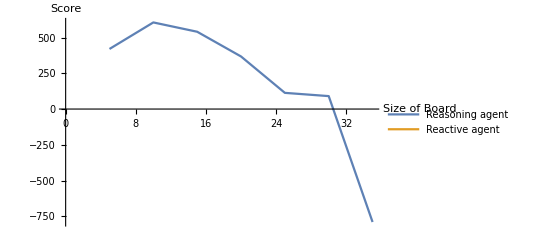

```mathematica
ListLinePlot[{NvS,NvSr}, AxesLabel->{"Size of Board","Score"},PlotLegends->{"Reasoning agent", "Reactive agent"}]
```